Define potential functions

```mathematica
U0[x_]:=x^2
U1[x_]:=c*x
```

solving for L_0(q_0)=0

```mathematica
DSolve[{q''[x]-2x*q'[x]==0,q[-1]==0,q[1]==1},q[x],{x,-1,1}]
```

{{q[x]→(Erfi[1]+Erfi[x])/(2 Erfi[1])}}

```mathematica
q0[x_]:=(Erfi[1]+Erfi[x])/(2 Erfi[1])
```

solving for L(q)=0

```mathematica
DSolve[{q''[x]-(2x+c)*q'[x]==0,q[-1]==0,q[1]==1},q[x],{x,-1,1}]
```

{{q[x]→(Erfi[1-c/2]+Erfi[c/2+x])/(Erfi[1-c/2]+Erfi[(2+c)/2])}}

```mathematica
qp[x_]:=(Erfi[1-c/2]+Erfi[c/2+x])/(Erfi[1-c/2]+Erfi[(2+c)/2])
```

solving for L_1(q_0)= - L_0(q_1)

```mathematica
DSolve[{q''[x]-(2x)*q'[x]==c*q0'[x],q[-1]==0,q[1]==0},q[x],{x,-1,1}]
```

{{q[x]→(c (-ⅇ+ⅇ^(x^2)))/(2 √π Erfi[1])}}

```mathematica
q1[x_]:=(c (-ⅇ+ⅇ^(x^2)))/(2 √π Erfi[1])
```

Plotting functions 
Case 1: c=0.1

```mathematica
c=0.1;
```

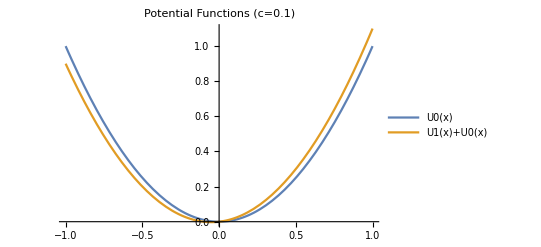

```mathematica
Plot[{U0[x],U1[x]+U0[x]},{x,-1,1},PlotLegends->"Expressions",PlotLabel->"Potential Functions (c=0.1)"]
```

```mathematica
q[x_]:=qp[x];
```

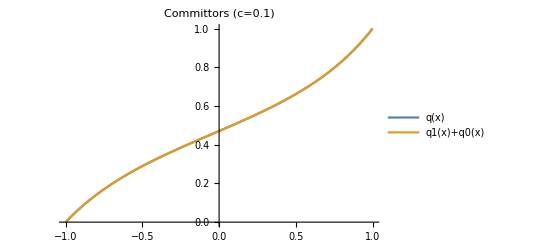

```mathematica
Plot[{q[x],q1[x]+q0[x]},{x,-1,1},PlotLegends->"Expressions",PlotLabel->"Committors (c=0.1)"]
```

Case 2: c=1

```mathematica
c=1;
```

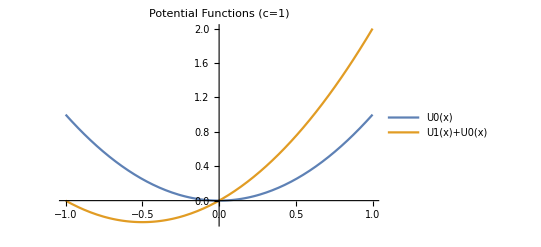

```mathematica
Plot[{U0[x],U1[x]+U0[x]},{x,-1,1},PlotLegends->"Expressions",PlotLabel->"Potential Functions (c=1)"]
```

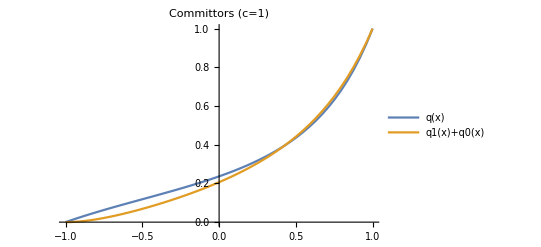

```mathematica
Plot[{q[x],q1[x]+q0[x]},{x,-1,1},PlotLegends->"Expressions",PlotLabel->"Committors (c=1)"]
```